```mathematica
levelNames ={"a1","a2","b1","b2"};
```

```mathematica
rootPath = NotebookDirectory[];
```

```mathematica
texts = Table[Import[ FileNameJoin[{rootPath , "data","sentences" ,StringJoin[ level," sentences.txt"]}]],{level,levelNames}];
```

```mathematica
TextSentences[texts[[1]],4]
```

{I would like that, my dear.,I would like to order  la carte.,I would like to compose a message.,Beautiful work.}

```mathematica
Flatten[TextSentences[#,2]&@texts]
```

{I would like that, my dear.,I would like to order  la carte.,That’s Speedy!,Carter laughing.,And guess what?,Catch you later!,He couldn't even guess.,He couldn't imagine it.}

```mathematica
sentences=TextSentences[#]&@texts;
```

```mathematica
nSents =1000;
```

```mathematica
sentencesShort = Map[Take[#,nSents]&,sentences];
```

```mathematica
nameLength={levelNames,Map[Length,sentencesShort]}ᵀ;
```

```mathematica
sent2d = DimensionReduce[Flatten[sentencesShort],2,Method->"TSNE"];
```

```mathematica
labels=Flatten[Table[Table[x[[1]],x[[2]]],{x,nameLength}]];
```

```mathematica
byLevels=GroupBy[Thread[sent2d->labels],Last->First];
```

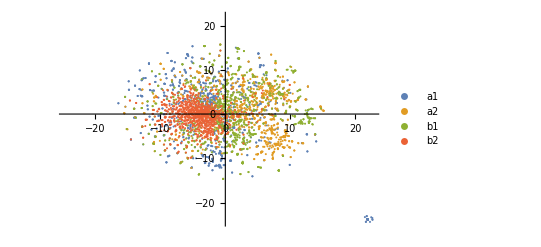

```mathematica
ListPlot[Values[byLevels],PlotLegends->Keys[byLevels]]
```